# Optimering

## Exempel från föreläsningen

#### Exempel 1

```mathematica
Remove["Global`*"]
f[x_,y_]=x*y^2;
Maximize[{f[x,y],x^2+y^2<=1,x>=0,y>=0},{x,y} ]
```

{2/(3 √3),{x→1/(√3),y→√(2/3)}}

#### Exempel 2

```mathematica
Remove["Global`*"]
f[x_,y_]=x^2+2x*y-3y^2;
v={1,-1}/Norm[{1,-1}];
G=Grad[f[x,y], {x,y}]
G.v/.{x->1,y->2}
```

{2 x+2 y,2 x-6 y}

8 √2

### Polynomapproximation

```mathematica
Remove["Global`*"]
xv={x1,x2,x3};
xv2=xv^2;
fv={f1,f2,f3};
const=Table[c[i],{i,0,2}];
p={1,x,x^2}.const
a=Transpose[ {{1,1, 1},xv,xv^2}];
sol=Solve[a.const==fv,const];
x4=Collect[FullSimplify[-c[1]/(2c[2])/.sol[[1]]],{f1,f2,f3}]
```

c[0]+x c[1]+x^2 c[2]

(f3 (x1-x2) (x1+x2)+f1 (x2-x3) (x2+x3)+f2 (-x1^2+x3^2))/(2 (f3 (x1-x2)+f1 (x2-x3)+f2 (-x1+x3)))

### Exempel 3

p2(x) = 3.-3.5 x+2.5 x^2, x4 = 0.7, p2_min = 1.775

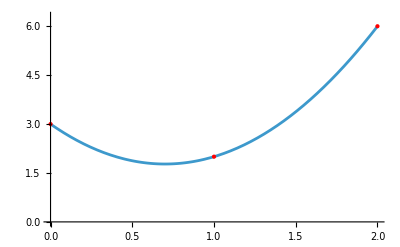

```mathematica
Remove["Global`*"]
xv={0.,1,2};
fv={3,2,6};
xv2=xv^2;
data=Transpose[{xv,fv}];
lp=ListPlot[data,PlotStyle->{Red,PointSize[Large]}];
const=Table[c[i],{i,0,2}];
a=Transpose[ {{1,1, 1},xv,xv^2}];
sol=Solve[a.const==fv,const][[1]];
p={1,x,x^2}.const/.sol;
x4=-c[1]/(2c[2])/.sol;
Print["p2(x) = ",p,", x4 = ",x4,", p2_min = ",p/.x->x4];
pl=Plot[p,{x,xv[[1]],xv[[3]]}, PlotRange->{0,6.3}];
Show[pl,lp]
```

### Exempel 4

{{x→0.666667}}

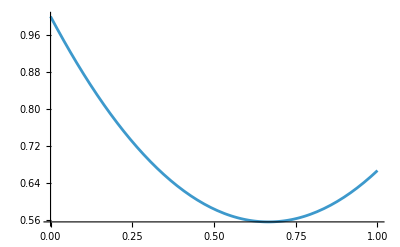

{0.,0.5,1}

{0.5,0.75,1}

{0.5,0.625,0.75}

{0.625,0.6875,0.75}

{0.625,0.65625,0.6875}

{0.65625,0.671875,0.6875}

{0.65625,0.664063,0.671875}

{0.664063,0.667969,0.671875}

{0.664063,0.666016,0.667969}

{0.666016,0.666992,0.667969}

{0.666016,0.666504,0.666992}

{0.666504,0.666748,0.666992}

{0.666504,0.666626,0.666748}

{0.555556,{x→0.666667}}

```mathematica
Remove["Global`*"]
f[x_]=x^2-4x/3+1;
NSolve[f'[x]==0,x]
eps=0.001;
{a,b}={0.,1};
Plot[f[x],{x,a,b}]
eps=0.0001;
c=(a+b)/2;
While[Abs[f'[c]]>eps,
c=(b+a)/2;
Print[{a,c,b}];
If [f'[c]>eps,b=c,a=c]
]
N[Minimize[f[x],x]]
```

### Exempel 5

```mathematica
Remove["Global`*"]
f[x_]=x^2-4x/3+1;
epsilon=0.000001;
diff=1.;
xold=1.;
While[diff>epsilon,
xnew=xold-f'[xold]/f''[xold];
diff=Abs[xnew-xold];
Print[{xnew,diff}];
xold=xnew;
]
f[xnew]
NMinimize[f[x],x]
```

{0.666667,0.333333}

{0.666667,0.}

0.555556

{0.555556,{x→0.666667}}

### Exempel 6

```mathematica
Remove["Global`*"]
f[x_,y_]:=(x+0.3y)^2+(2(x^2+y^2-1)-1)^2;
Plot3D[f[x,y],{x,-1.3,1.8},{y,0.5,1.7},ColorFunction->Hue]
FindMinimum[f[x,y],{{x,-1.1},{y,0.8}}]
```

-Graphics3D-

{4.47878×10^-19,{x→-0.351928,y→1.17309}}

∇f = {16. (x^3+0.0375 y+x (-1.375+y^2)),16. (0.0375 x-1.48875 y+x^2 y+y^3)}

H = {{-22+48 x^2+16 y^2,0.6+32 x y},{0.6+32 x y,48. (-0.49625+0.333333 x^2+y^2)}}

Route = {{-1.1,-0.928934,-0.706371,-0.545316,-0.432761,-0.377824,-0.35827,-0.353271,-0.3522,-0.351982,-0.351939},{0.8,0.858773,1.04653,1.1184,1.15598,1.16842,1.17203,1.17287,1.17305,1.17308,1.17309}}

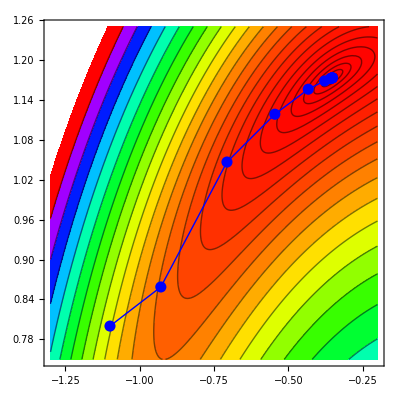

fmin = 1.79546×10^-10

```mathematica
Remove["Global`*"]
f=(x+0.3y)^2+(2(x^2+y^2-1)-1)^2;
alpha=0.8;
Print["∇f = ",G=FullSimplify[D[f,{{x,y}}]]];
Print["H = ",H=FullSimplify[D[f,{{x,y},2}]]];
{x,y}={-1.1,0.8};
route={{x,y}};
Do[{x,y}={x,y}-alpha*Inverse[H].G;AppendTo[route,{x,y}],{10}];
Print["Route = ",Transpose[route]];
ContourPlot[f,{x,-1.3,-0.2},{y,0.75,1.25},
Contours-> 6(Range[0,6,0.25]/6)^4,
PlotPoints->50, 
ColorFunction->Hue,
Epilog->{Blue,Line[route],PointSize[0.02],Point/@ route}
]
Print["fmin = ",f]
```

#### Exempel 7

```mathematica
Remove["Global`*"]
f=x^2+y^2+z^2;
g=x-y+2z-6;
L=f+λ*g
G=D[L,{{x,y,z,λ}}]
sol=Solve[G==0,{x,y,z,λ}]
f/.sol[[1]]
Minimize[{f,g==0},{x,y,z}]
```

x^2+y^2+z^2+(-6+x-y+2 z) λ

{2 x+λ,2 y-λ,2 z+2 λ,-6+x-y+2 z}

{{x→1,y→-1,z→2,λ→-2}}

6

{6,{x→1,y→-1,z→2}}

#### Exempel 8

```mathematica
Remove["Global`*"]
f=x^2+y^2+z^2;
g1=x+y+z+3;
g2=x+2y+3z-6;
vars={x,y,z,λ1,λ2};
L=f+λ1*g1+λ2*g2;
G=D[L,{vars}];
H=D[L,{vars,2}];
invH=Inverse[H] ;(*H konstant, invH behöver bara beräknas 1 gång!*)
epsilon=0.000001;
diff=1;
xold={1,1,1,1,1};
While[diff>epsilon,
xnew=xold-invH.G/.Thread[vars->xold];
diff=Norm[xnew-xold];
Print[{xnew,diff}];
xold=xnew;
]
Print["(x,y,z) = ",xnew,", f_min = ",f/.Thread[vars->xold]]
Minimize[{f,g1==0,g2==0},{x,y,z}]
```

{{-7,-1,5,26,-12},√878}

{{-7,-1,5,26,-12},0}

(x,y,z) = {-7,-1,5,26,-12}, f_min = 75

{75,{x→-7,y→-1,z→5}}

#### Exempel 10

```mathematica
Remove["Global`*"]
f=x^2+y^2+z^2;
g1=x+y+z+3;
g2=x+2y+3z-6.;
vars={x,y,z};
P=f+1/r(g1^2+g2^2)/.r->10^(-5)
G=D[P,{vars}];
H=D[P,{vars,2}];
sol=Solve[G==0,vars]
f/.sol[[1]]
Minimize[{f,g1==0,g2==0},{x,y,z}]
```

x^2+y^2+z^2+100000 ((3+x+y+z)^2+(-6.+x+2 y+3 z)^2)

{{x→-6.9998,y→-0.999957,z→4.99988}}

74.9959

{75.,{x→-7.,y→-1.,z→5.}}